```mathematica
spfan=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n-xi3.wdx"];
f2n=Flatten[Query[2,1]@spfan,1];
g2n=Flatten[Query[2,2]@spfan,1];
```

```mathematica
lf2n=Interpolation[f2n];
sf2[x_]=lf2n[x,-1];
```

```mathematica
NIntegrate[sf2[x],{x,0.3,1}]
```

1.11907

```mathematica
(*ERBLpart*)
```

```mathematica
Hqz1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(1/2*2.6*β^(0.75-1)(1-β)^0.95+1/6*0.21/Beta[0.5+1,8+1] β^(0.5-1)(1-β)^8)/(1-t/λ1^2);
Hqf1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(-1/6*0.21/Beta[0.5+1,8+1] Abs[β]^(0.5-1)*(1-Abs[β])^8)/(1-t/λ1^2);
Hqf2=(Hqf1/.{α->(x-β)/ξ})/ξ;
Hqz2=(Hqz1/.{α->(x-β)/ξ})/ξ;
Hqfn2[x_]=Hqf2/.{b0->2,ξ->0.3/y,x->x/y,λ1->0.79,t->-1};
Hqzn2[x_]=Hqz2/.{b0->2,ξ->0.3/y,x->x/y,λ1->0.79,t->-1};
```

```mathematica
Hf2qf[x_]=Hqfn2[x]*sf2[y]/y;
Hf2qz[x_]=Hqzn2[x]*sf2[y]/y;
```

```mathematica
(*注意这里sf2是已经完成了k和θ积分的*)
```

```mathematica
InHf2q[x_]:=NIntegrate[Hf2qf[x],{y,0.3,1},{β,(x-0.3)/(y+0.3),0}]+NIntegrate[Hf2qz[x],{y,0.3,1},{β,0,(x+0.3)/(y+0.3)}];
```

```mathematica
InHf2q[0.1]
```

1.34828

```mathematica
Table[{x,InHf2q[x]},{x,-0.3,0.3,0.01}];
```

```mathematica
pf=%25;
```

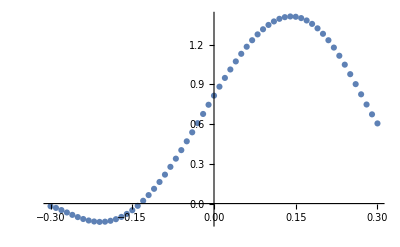

```mathematica
ListPlot[pf]
```

```mathematica
(*DGLAPpart*)
Hq1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ1^2);
Hqa=(Hq1/.{α->(x-β)/ξ})/ξ;
Hqan=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3,x->0.5};
Hqay[x_]=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3/y,x->x/y};
Hf2q[x_]=Hqay[x]*sf2[y]/y;
InHf2qD[x_]:=NIntegrate[Hf2q[x],{y,x,1},{β,(x-0.3)/(y-0.3),(x+0.3)/(y+0.3)}];
```

```mathematica
InHf2qD[0.5]
```

0.0399664

```mathematica
Parallelize[pfd=Table[{x,InHf2qD[x]},{x,0.3,1,0.01}]];
```

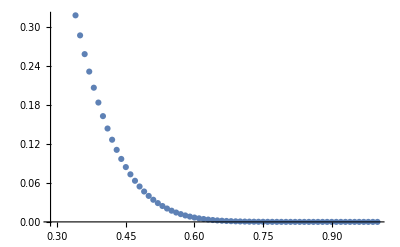

```mathematica
ListPlot[pfd]
```

```mathematica
(*真正的3d图*)
```

```mathematica
Ef3df[x_,t_]=Hqfn2[x]*lf2n[y,t]/y;
Ef3dz[x_,t_]=Hqzn2[x]*lf2n[y,t]/y;
Df3d[x_,t_]=Hqay[x]*lf2n[y,t]/y;
```

```mathematica
NIntegrate[Df3d[0.5,-1],{y,0.5,1},{β,(0.5-0.3)/(y-0.3),(0.5+0.3)/(y+0.3)}]
```

0.0399664

```mathematica
Dinf3d[x_,t_]:=NIntegrate[Df3d[x,t],{y,x,1},{β,(x-0.3)/(y-0.3),(x+0.3)/(y+0.3)}];
Einf3d[x_,t_]:=NIntegrate[Ef3df[x,t],{y,0.3,1},{β,(x-0.3)/(y+0.3),0}]+NIntegrate[Ef3dz[x,t],{y,0.3,1},{β,0,(x+0.3)/(y+0.3)}];
```

```mathematica
Einf3d[0.1,-1]
```

1.34828

```mathematica
Dinf3d[0.5,-1]
```

0.0399664

```mathematica
Parallelize[lfD3d=Table[{{x,t},Dinf3d[x,t]},{x,0.3,1,0.005},{t,-1,-0.3488127032967032,0.01}]];(*about 2 hours*)
```

```mathematica
tsetfD=Interpolation[Flatten[lfD3d,1]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[tsetfD[x,y],{x,0.3,1.},{y,-1.,-0.35},PlotRange->All]
```

-Graphics3D-